The goal of this notebook is simply to collect and organize all of the work that Vijay has already done in the various other Mathematica notebooks. This will hopefully be useful as a check by a second pair of eyes, and as a confirmation that all of our numbers and plots are up-to-date and final with our current understanding of physics.

```mathematica
ConvertMeV2ToMeVPerTrigger=Quantity[1.,"Megaelectronvolts"]^2/Quantity[1/10^-5,("Megaelectronvolts")/("Centimeters")] Quantity[1.,"SpeedOfLight"*"ReducedPlanckConstant"]^-1//UnitConvert
```

506773.

```mathematica
ConvertBarnToMeV=Quantity[1.,"Barns"]/Quantity[1.,("Megaelectronvolts")^-2] Quantity[1.,"SpeedOfLight"*"ReducedPlanckConstant"]^-2//UnitConvert
```

0.00256819

# Scratch

```mathematica
(Z^2 α)/n^(-1/3)/.{Z->ZCarbon,α->αval,n->nIonMeV[1.37]}
```

36/137 nIonMeV[1.37]^(1/3)

```mathematica
cs(6π n)^(1/3)/.{cs->0.01,n->nIonMeV[1.37]}
```

0.0266134 nIonMeV[1.37]^(1/3)

# White dwarf parameters

Here we define various physical parameters of the white dwarf, which are used frequently in this notebook. They are defined as functions of white dwarf mass or density, where appropriate.

Let’s say that the following are the minimum and maximum white dwarf masses of interest, which are ultimately what we care about for plotting and discussion.

```mathematica
Mmin=0.85;
Mmax=1.37;
```

Some useful values:

```mathematica
mCarbon=12*10^3(* MeV *);
ZCarbon=6;
αval=1/137;
mNeutron=940;
mProton=938;
mPion=140;
mElectron=0.5;
```

## White dwarf mass and radius data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/priggins/Dropbox/Berkeley-current/Research/WhiteDwarfParticleDetector/Qballs

Density-mass relation and number densities

## Density-mass relation

Density-mass relation and its inverse, with density in g/cm^3 and mass in M_☉.

```mathematica
WDLogDensityMassData=Import["WD.csv"];
WDDensityMassData={10^(#[[1]]),#[[2]]}&/@WDLogDensityMassData;
WDDensityMassCGS=Interpolation[WDDensityMassData]
WDMassDensityCGS=Interpolation[Reverse/@WDDensityMassData]
```

10
InterpolatingFunction[{{11437.4, 5.43438 10  }}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Similarly, with densities in units of MeV^4,

```mathematica
Quantity[1.,"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)]//UnitConvert
```

4.31013×10^-6

```mathematica
WDDensityMassDataInMeV={Quantity[#[[1]],"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)],#[[2]]}&/@WDDensityMassData;
WDDensityMassMeV=Interpolation[WDDensityMassDataInMeV]
WDMassDensityMeV=Interpolation[Reverse/@WDDensityMassDataInMeV]
```

InterpolatingFunction[{{0.0492968, 234229.}}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Some example densities as functions of mass:

```mathematica
{WDMassDensityCGS[0.85],WDMassDensityCGS[1.25],WDMassDensityCGS[1.37]}
{WDMassDensityMeV[0.85],WDMassDensityMeV[1.25],WDMassDensityMeV[1.37]}
```

{1.44744×10^7,2.88397×10^8,3.22949×10^9}

{62.3864,1243.03,13919.5}

## Ion and electron number densities

We know compute the ion and electron number densities as a function of white dwarf mass. Note that our ions are carbon with mass = 12*m_p and charge Z=6.

### Ion number density

In units of cm^-3,

```mathematica
nIonCGS[M_]:=WDMassDensityCGS[M] Quantity[1.,"Grams"]/Quantity[12,"ProtonMass"];
Table[nIonCGS[M],{M,{0.85,1.25,1.37}}]
```

{7.21141×10^29,1.43685×10^31,1.609×10^32}

And in units of MeV^3,

```mathematica
nIonMeV[M_]:=WDMassDensityMeV[M] Quantity[1.,"Megaelectronvolts"]/Quantity[12,"Gigaelectronvolts"];
Table[nIonMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.00519886,0.103586,1.15996}

```mathematica
nIonMeV[1.4]
```

13.7133

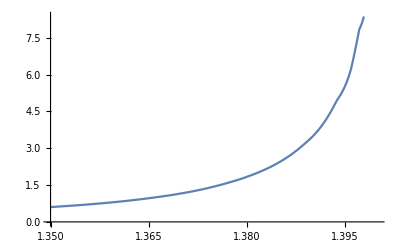

```mathematica
Plot[nIonMeV[Mwd],{Mwd,1.35,1.4}]
```

### Electron number density

In units of cm^-3,

```mathematica
nElectronCGS[M_]:=nIonCGS[M]*Z/.{Z->ZCarbon};
Table[nElectronCGS[M],{M,{0.85,1.25,1.37}}]
```

{4.32685×10^30,8.62111×10^31,9.65397×10^32}

And in units of MeV^3,

```mathematica
nElectronMeV[M_]:=nIonMeV[M]*Z/.{Z->ZCarbon};
Table[nElectronMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.0311932,0.621515,6.95976}

In the Fermi sea, the electron number density is reduced. A particle transferring energy ω to an electron in the Fermi sea sees an effective electron density of

```mathematica
Integrate[ϵ^2/π^2,{ϵ,Ef-ω,Ef}]//FullSimplify
```

(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2)

Note when ω=E_f, this is the full electron density:

```mathematica
Integrate[ϵ^2/π^2,{ϵ,0,Ef}]/.Ef->(3 π^2 ne)^(1/3)
```

ne

So we can define an effective density

```mathematica
nElectronEffective[ω_,Mwd_]:=Piecewise[{
{nElectronMeV[Mwd],ω≥EFermiMeV[Mwd]},
{(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2)/.Ef->EFermiMeV[Mwd],ω<EFermiMeV[Mwd]}
}];
```

This is given approximately by a linear reduction below the Fermi energy:

```mathematica
nElectronEffectiveApprox[electronEnergy_,Mwd_]:=Piecewise[{
{nElectronMeV[Mwd],electronEnergy≥EFermiMeV[Mwd]},
{nElectronMeV[Mwd] electronEnergy/EFermiMeV[Mwd],electronEnergy<EFermiMeV[Mwd]}
}];
```

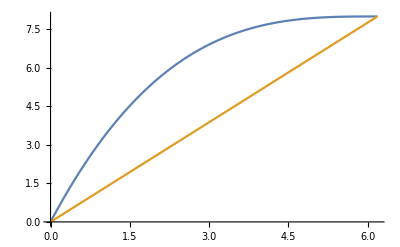

```mathematica
PlotTEMP[{(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2),n ω/Ef},{ω,0,Ef}]//.{Ef->(3 π^2 n)^(1/3),n->8}/.PlotTEMP->Plot
```

Mass-radius relation and escape velocity

## Mass-radius relation

Mass-radius relation and its inverse, with mass in M_☉ and radius in km. (The radius is originally in R_☉ in the data file, which must be converted.).

```mathematica
WDMassRadiusData=Import["WDradius.csv"];
WDMassRadiusDataConvertedToKilometers={1,Quantity[1.,"SolarRadius"]/Quantity[1.,"Kilometers"]}*#&/@WDMassRadiusData;
WDMassRadius=Interpolation[WDMassRadiusDataConvertedToKilometers]
WDRadiusMass=Interpolation[Reverse/@WDMassRadiusDataConvertedToKilometers]
```

InterpolatingFunction[{{0.0407984, 1.42331}}, <>]

InterpolatingFunction[{{328.863, 19770.4}}, <>]

## Escape velocity

Here is the escape velocity as a fraction of c, again as a function of white dwarf mass.

```mathematica
vesc[M_]:=1/c √((2G Mwd)/R)/.
{G->Quantity[1.,"GravitationalConstant"],
R->Quantity[WDMassRadius[M],"Kilometers"],
Mwd->Quantity[M,"SolarMass"],
c->Quantity[1.,"SpeedOfLight"]}//UnitConvert;
Table[vesc[M],{M,{0.85,1.25,1.37}}]
```

{0.0198225,0.0333143,0.0463183}

## Plasma and Lattice parameters

Fermi energy:

```mathematica
EFermiMeV[Mwd_]:=(3 π^2 nElectronMeV[Mwd])^(1/3);
```

Thomas-Fermi length:

```mathematica
λThomasFermi[Mwd_]:=(Ef/(6π Z α ne))^(1/2)/.{Ef->EFermiMeV[Mwd],ne->nElectronMeV[Mwd],Z->ZCarbon,α->αval};
```

Plasma frequency:

Debye energy:

# Trigger size and boom energies

Here we calculate the trigger size and minimum energy deposits necessary for explosion as functions of white dwarf density and mass.

## Trigger size

Here is the trigger size in cm^-3 as a function of white dwarf density and mass:

```mathematica
triggerDensityCGS[ρCGS_]:=
Return@If[ρCGS>10^8,10^-5*(ρCGS/(5*10^9))^(-1/2),1/(10000 √2)*(ρCGS/10^8)^-2];
triggerMass[M_]:=Module[{ρ},
ρ=WDMassDensityCGS[M];
Return@If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
];
```

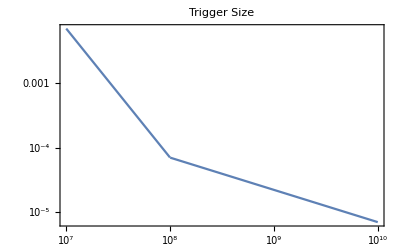

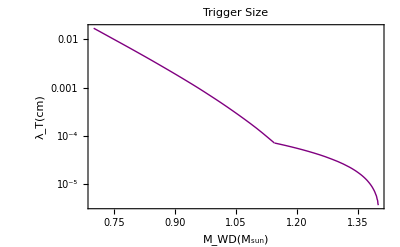

```mathematica
LogLogPlot[{triggerDensityCGS[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggerMass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

```mathematica
Table[Quantity[triggerMass[M],"Centimeters"],{M,{0.85,1.25,1.37}}]//ScientificForm
```

{3.3751×10^-3 cm,4.1638×10^-5 cm,1.24428×10^-5 cm}

## E_boom

The minimum energy deposit necessary to explode the white dwarf is given here in GeV as a function of white dwarf mass:

```mathematica
eboom[M_]:=Log10[(nIonCGS[M]*(4π)/3(λT)^3 Tmin)/Quantity[1.,"Gigaelectronvolts"]]/.{λT->triggerMass[M],Tmin->Quantity[1.,"Megaelectronvolts"]};
```

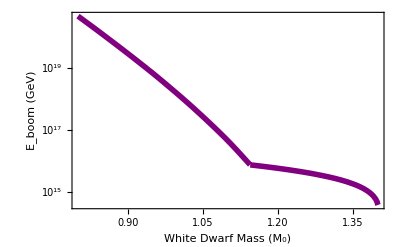

```mathematica
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
YEboom = {{15, ""}, {16, ""},{17, ""}, {18, ""}, {19, ""},  {20,""},{21, ""},{22, ""},{23, ""}};
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,YEboom},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

```mathematica
Table[Quantity[10^eboom[M],"Gigaelectronvolts"],{M,{0.85,1.25,1.37}}]
```

{1.16136×10^20 GeV,4.34479×10^15 GeV,1.29837×10^15 GeV}

# Collision processes and stopping powers

Here we gather and compute the stopping powers for all the various collision processes (Coulomb, hadronic shower, etc.) that energetic particles in a white dwarf might undergo.

## Nuclear interactions

Low-energy elastic scatters

Once pions and nucleons have sufficiently low-energy (below 10 MeV), they can hadronically scatter of ions either elastically (transferring a fraction of their kinetic energy and then bouncing off).

## Bounce-counting method

At this point, the particles are non-relativistic. Conservation of momentum and energy demands

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

The second solution is the physical one, so the incident particle has final energy

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

assuming the incident particle had initial energy ϵ. The incident particle retains a fraction of its initial energy given by

```mathematica
Eretained=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

The average fraction ζ retained, considering all possible angles of scatter and assuming the particle scatters isotopically, is

```mathematica
ζel=1/(2Pi)Integrate[Eretained,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

A proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei, so our estimate here is good.

Since a light incident particle retains most of its energy after collision with a heavy incident particle, it will perform a random walk with several collisions before it has transferred O(1) of its initial energy. The number of steps nn is

```mathematica
Solve[ζel^nn==0.1/.{M->mCarbon,m->mPion},nn]//Quiet(* pion *)
```

{{nn→99.2568}}

```mathematica
Solve[ζel^nn==0.1/.{M->mCarbon,m->mNeutron},nn]//Quiet(* neutron/proton, ignoring electromagnetic scatters *)
```

{{nn→15.2658}}

Since this is a random walk, the particle will travel a distance √nn λ, where λ=(n_ion σ)^-1 is the mean free path. The stopping powers are therefore

```mathematica
dEdxElasticMeson=Piecewise[{{ϵ/(nn(nion*σElasticMeson)^-1)/.nn->100,ϵ≤10},{0,ϵ>10}}];
dEdxElasticNucleon=Piecewise[{{ϵ/(nn(nion*σElasticNucleon)^-1)/.nn->10,ϵ≤10},{0,ϵ>10}}];
```

## Free particle structure factor method

At this point, the particles are non-relativistic. Conservation of momentum and energy demands

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

The second solution is the physical one, so the incident particle has final energy

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
Efin//FullSimplify
```

(m (√2 m √(ϵ/m) Cos[θ]+√(-m ϵ+(2 M^2 ϵ)/m+m ϵ Cos[2 θ]))^2)/(2 (m+M)^2)

The maximum energy transfer is

```mathematica
ϵ-Efin/.θ->π//FullSimplify[#,M>0]&
```

(4 m M ϵ)/(m+M)^2

The free particle dσ/dω for a non-relativistic neutron scattering on targets of mass M is given by

```mathematica
dσdωNeutronElastic=(2π M b^2)/k^2/.b->√(σ/(4π))
```

(M σ)/(2 k^2)

Note σ is approximately the total free particle scattering cross section:

```mathematica
σFreeNeutron=Integrate[dσdωNeutronElastic/.k->√(2m ϵ),{ω,0,(4 m M ϵ)/(m+M)^2}]
```

(M^2 σ)/(m+M)^2

The stopping power is then

```mathematica
Integrate[dσdωNeutronElastic n ω/.k->√(2m ϵ),{ω,0,(4 m M ϵ)/(m+M)^2}]
```

(2 m M^3 n ϵ σ)/(m+M)^4

Or in terms of the free cross section σ_f,

```mathematica
(2 m M^3 n ϵ σ)/(m+M)^4/.First@Solve[σFreeNeutron==σf,σ]
```

(2 m M n ϵ σf)/(m+M)^2

For a neutron or proton, the stopping power is

```mathematica
(2 m M n ϵ σf)/(m+M)^2/.{M->mCarbon,m->mNeutron}//N
```

0.134732 n ϵ σf

For a pion,

```mathematica
(2 m M n ϵ σf)/(m+M)^2/.{M->mCarbon,m->mPion}//N
```

0.0227983 n ϵ σf

These very similar to the bounce-counting results.

## Plots

Putting the stopping powers in a for amenable to plotting (using the structure factor results), we find for neutrons and protons

```mathematica
dEdxElasticNucleon[ϵ_,Mwd_]:=Piecewise[{{(2 m M n ϵ σf)/(m+M)^2,1<ϵ<10},{0,ϵ>10}}]/.{M->mCarbon,m->mNeutron,n->nIonMeV[Mwd],σf->1*ConvertBarnToMeV};
```

and for pions

```mathematica
dEdxElasticPion[ϵ_,Mwd_]:=Piecewise[{{(2 m M n ϵ σf)/(m+M)^2,1<ϵ<10},{0,ϵ>10}}]/.{M->mCarbon,m->mPion,n->nIonMeV[Mwd],σf->1*ConvertBarnToMeV};
```

Nucleon plot matches well ....

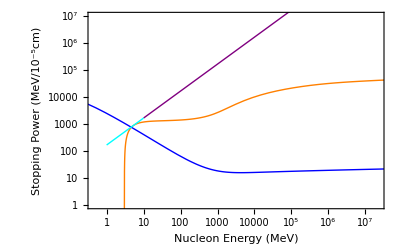
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticNucleon[ϵ,1.37],{ϵ,1,10}],-Graphics-]
```

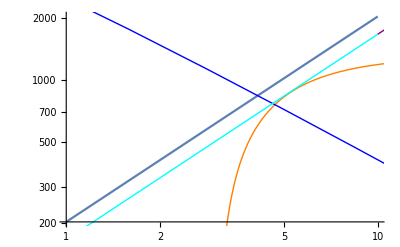

as does the pion plot ...

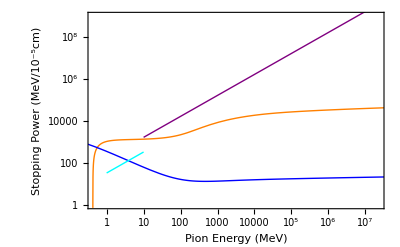
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticPion[ϵ,1.37],{ϵ,1,10}],-Graphics-]
```

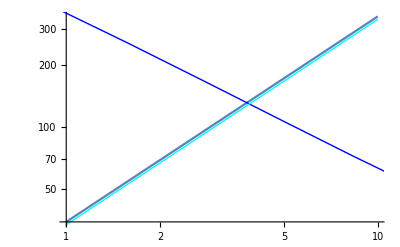

### Low densities

```mathematica
nElectronMeV[0.85]
```

0.0311932

Nucleon plot matches well ....

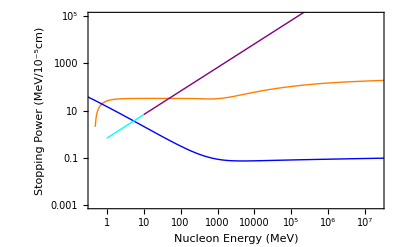
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticNucleon[ϵ,0.85],{ϵ,1,10}],-Graphics-]
```

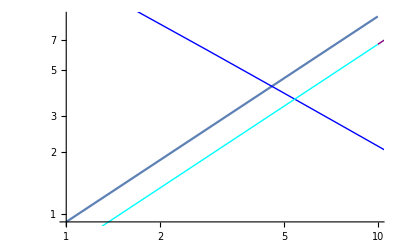

as does the pion plot ...

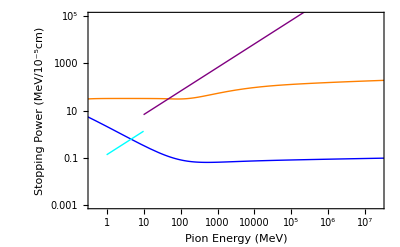
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticPion[ϵ,0.85],{ϵ,1,10}],-Graphics-]
```

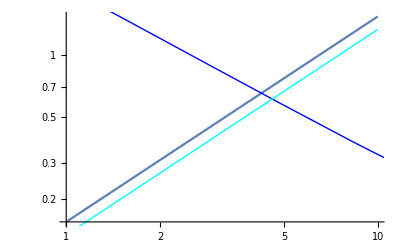

Low-energy inelastic scatters

In principle, a neutron or pion could also be inelastically absorbed by the ion. The neutron capture cross section for carbon is famously low, which is why it is useful as a moderator for nuclear reactors. There is a 3 order of magnitude difference between the scattering and capture cross-sections for neutrons in carbon.

As for pions ...... also probably insignificant compared to elastic scatters.

Phonon production

Not important.

Nonelastic scatters / Hadronic showers

When the energy is too high, the particles will non-elastically scatter instead, disintegrating the ions they hit:

```mathematica
dEdxNonelastic[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σNonelastic)^-1,ϵ>10},{0,ϵ≤10}}]/.{n->nIonMeV[Mwd],σNonelastic->0.1*ConvertBarnToMeV};
```

Nucleons match well ...

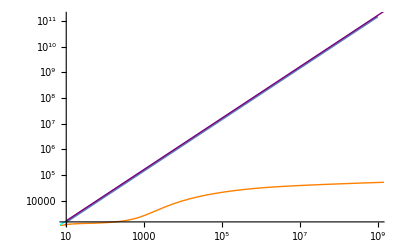

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

As do pions .... (good, because it’s the same curve ...)

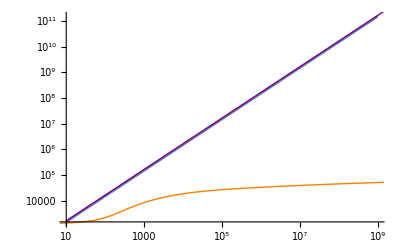

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

### low densities

Nucleons match well ...

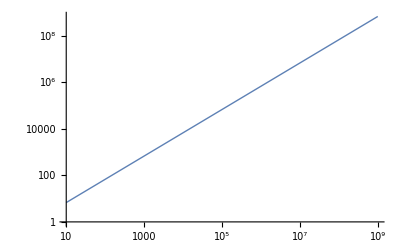

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thick]
```

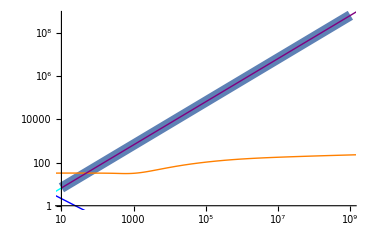

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[.02]],-Graphics-]
```

As do pions .... (good, because it’s the same curve ...)

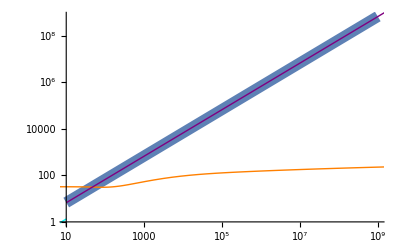

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[.02]],-Graphics-]
```

Photonuclear and electronuclear interactions

## Photonuclear

At high enough energies, photons can produce quark-anti-quark pairs and disintegrate a nucleus. The corresponding stopping power is

```mathematica
dEdxPhotonuclear[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σγA)^-1,ϵ>10},{0,ϵ≤10}}]/.{n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV};
```

This matches well.

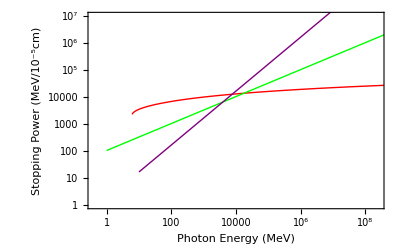
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPhotonuclear[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

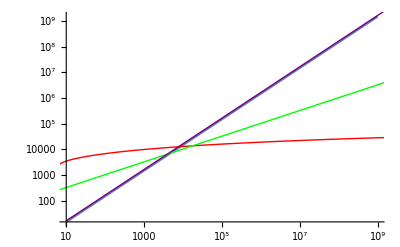

### low densities

This matches well.

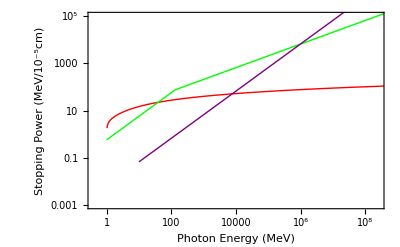
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPhotonuclear[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[0.02]],-Graphics-]
```

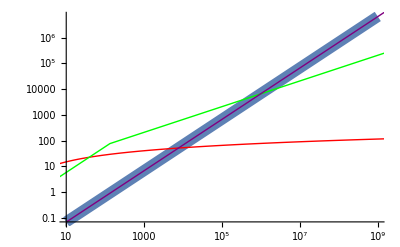

## Electronuclear

At high enough energies, electrons can produce virtual photons that can disintegrate a nucleus via photonuclear interaction. The corresponding stopping power is

```mathematica
dEdxElectronuclear[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σeA)^-1,ϵ>10},{0,ϵ≤10}}]//.{n->nIonMeV[Mwd],σeA->10α σγA,α->αval,σγA->0.001*ConvertBarnToMeV};
```

This matches well.

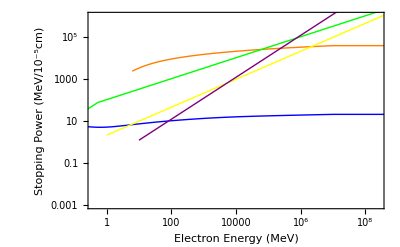
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElectronuclear[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

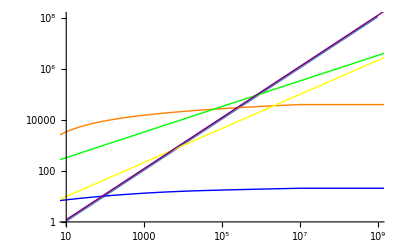

### low densities

This matches well.

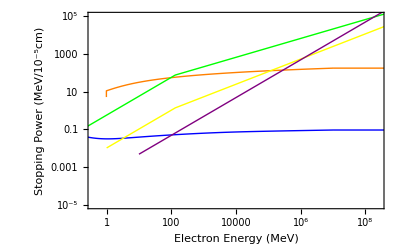
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElectronuclear[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[0.02]],-Graphics-]
```

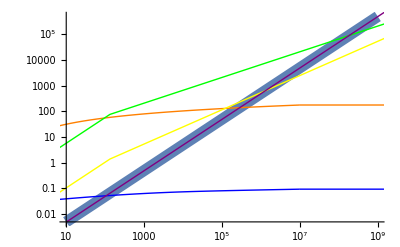

## EM interactions

Coulomb collisions of hadrons off ions

The Coulomb energy transfer cross section for a target with charge ±1 scattering off an ion with charge Z is

```mathematica
dσdωCoulomb[ω_]:=(2π Z^2 α^2)/(M β^2)1/ω^2(1-β^2 ω/ωKIN);
```

Picking the max energy transfer as the kinematically allowed maximum, and the minimum as set by the screening length, we find

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,ωSCR,ωKIN},Assumptions->{ωSCR>0,ωKIN>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (β^2 (-ωKIN+ωSCR)+ωKIN Log[ωKIN/ωSCR]))/(M β^2 ωKIN)

So the stopping power is approximately

```mathematica
(2 n π Z^2 α^2)/(M β^2)(Log[ωKIN/ωSCR]-1)
```

(2 n π Z^2 α^2 (-1+Log[ωKIN/ωSCR]))/(M β^2)

but we will use the more exact form here:

```mathematica
dEdxCoulombHadronsOffIonsSymbolic=(2 n π Z^2 α^2 (β^2 (-ωKIN+ωSCR)+ωKIN Log[ωKIN/ωSCR]))/(M β^2 ωKIN);
```

The maximum kinematically allowed energy transfer (corresponding to a backwards scatter) is

```mathematica
ωkin[ϵ_,m_,M_]:=(2M β^2 γ^2)/(1+2γ M/m+(M/m)^2)//.{β->√(1-γ^-2),γ->ϵ/m+1};
```

#### [Derivation]

```mathematica
Solve[{√(ki^2+m^2)==√(kf^2+m^2)+√(p^2+M^2),ki==kf Cos[θ]+p Cos[ψ],0==kf Sin[θ]-p Sin[ψ]}/.θ->π,kf,{ψ,p}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{kf→-(2 ki m^2-ki M^2+√(-(ki^2+m^2) M^2 (4 m^2-M^2)))/(2 m^2)},{kf→(√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))/(2 m^2)}}

```mathematica
√(ki^2+m^2)-√(kf^2+m^2)/.{kf->(√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))/(2 m^2)}//FullSimplify
```

√(ki^2+m^2)-√(m^2+((√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))^2)/(4 m^4))

```mathematica
Solve[{γi m+M==γf m+γM M,γi βi m==-γf βf m+γM βM M,γM==(1-βM^2)^(-1/2),γf==(1-βf^2)^(-1/2)},γf,{γM,βM,βf}]//FullSimplify
```

{{γf→((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)+√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))},{γf→((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)-√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))}}

```mathematica
m(γi-γf)/.{γf->((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)-√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))}/.γi->(1-βi^2)^(-1/2)//FullSimplify[#,{γi>0,βi>0,m>0,M>0,βi<1}]&
```

-(2 m^2 M βi^2)/(-2 m M √(1-βi^2)+m^2 (-1+βi^2)+M^2 (-1+βi^2))

```mathematica
-(2 m^2 M β^2)/(-2 m M √(1-βi^2)+m^2 (-1+βi^2)+M^2 (-1+βi^2))/.βi->√(1-1/γ^2)//FullSimplify[#,γ>0]&
```

(2 m^2 M β^2 γ^2)/(m^2+M^2+2 m M γ)

#### [Continuing ...]

The minimum energy transfer (ignoring lattice effects) corresponds to a soft scatter at the screening length. Estimating the energy transfer as (Δp)^2/(2M)∼(F Δt)^2/(2M)∼(((Z α)/b^2 b/β)^2)/(2M), we find

```mathematica
ωscr[ϵ_,m_,M_,Mwd_]:=(Z^2 α^2)/(b^2 β^2 M)//.{b->λThomasFermi[Mwd],Z->ZCarbon,α->αval,Ef->EFermiMeV[Mwd],ne->nElectronMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}
```

So the stopping power is

```mathematica
dEdxCoulombHadronsOffIons[ϵ_,m_,Mwd_]:=dEdxCoulombHadronsOffIonsSymbolic//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
M->mCarbon,Z->ZCarbon,n->nIonMeV[Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1};
```

### Pions off ions

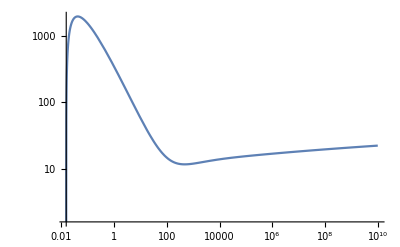

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mPion,1.37],{ϵ,.001,10^10},PlotRange->All]
```

Comparing to Vijay’s results, these match well

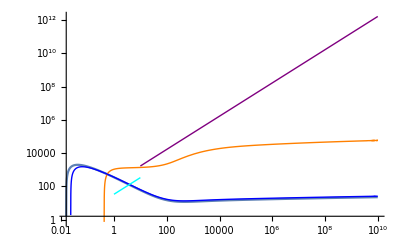

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

#### Low densities

Comparing to Vijay’s results, these match well

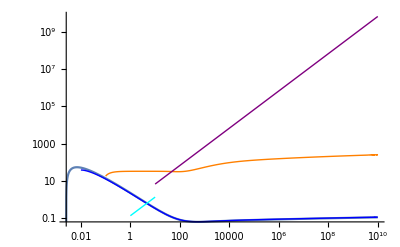

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mPion,0.85],{ϵ,.0001,10^10},PlotRange->All],-Graphics-,PlotRange->All]
```

### Protons off ions

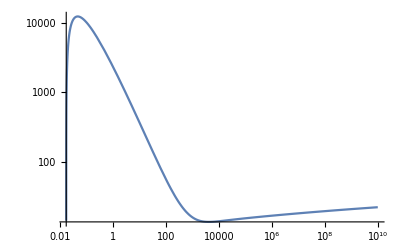

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mProton,1.37],{ϵ,.001,10^10},PlotRange->All]
```

Comparing to Vijay’s results, these match well

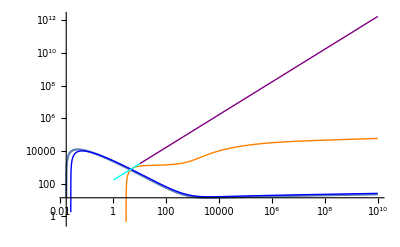

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

#### Low densities

Comparing to Vijay' s results, these match well

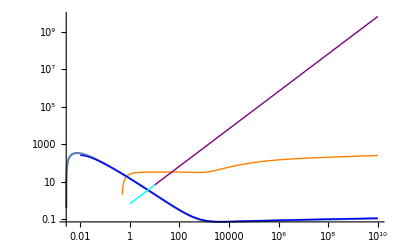

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mProton,0.85],{ϵ,.001,10^10},PlotRange->All],-Graphics-,PlotRange->All]
```

Coulomb collisions of electrons off ions

The derivation here is similar to the one for hadrons off ions, except we need to account for the possible degeneracy of the electrons after scattering

The Coulomb energy transfer cross section for a target with charge ±1 scattering off an ion with charge Z is

```mathematica
dσdωCoulomb[ω_]:=(2π Z^2 α^2)/(M β^2)1/ω^2(1-β^2 ω/ωKIN);
```

Picking the max energy transfer as the kinematically allowed maximum OR the maximum before the target particle would fall below the Fermi sea (whichever is smaller), and the minimum as set by the screening length, we find

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,ωSCR,Min[ϵ-Ef,ωKIN]},Assumptions->{ωSCR>0,ωKIN>ωSCR,ϵ-Ef>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[-Ef+ϵ,ωKIN]/ωSCR]-β^2 Min[-Ef+ϵ,ωKIN]))/(M β^2 ωKIN)

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIonsSymbolic[ϵ_]:=(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[-Ef+ϵ,ωKIN]/ωSCR]-β^2 Min[-Ef+ϵ,ωKIN]))/(M β^2 ωKIN);
```

The kinematic maximum and screening energies are the same as before.

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIons[ϵ_,Mwd_]:=dEdxCoulombElectronsOffIonsSymbolic[ϵ]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
m->mElectron,M->mCarbon,Z->ZCarbon,n->nIonMeV[Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1};
```

### Electrons off ions

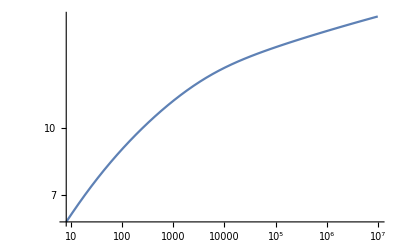

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7}]
```

Comparing to Vijay’s results, we see they match pretty well. The difference seems to be entirely from me preserving the -1 with the log, though there are also slight differences in the densities we’re computing things at.

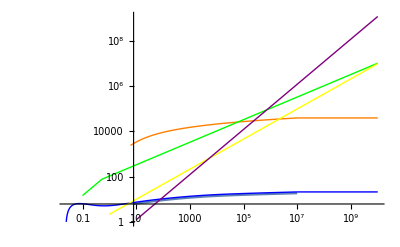

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

This is the same as if we had just used the hadron result, since the process is dominated by soft scatters:

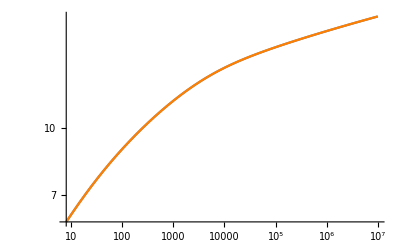

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7}],
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mElectron,1.37],{ϵ,8,10^7},PlotStyle->Orange]]
```

#### Low densities

Again these match well

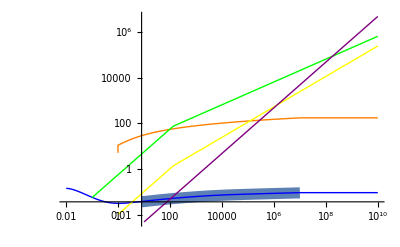

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,0.85],{ϵ,8,10^7},PlotStyle->Thickness[0.02]],-Graphics-,PlotRange->All]
```

Coulomb collisions of hadrons off electrons

The derivation for coulomb collisions off electrons is the same as hadrons off ions, except with different target number density.

```mathematica
dEdxCoulombHadronsOffElectrons[ϵ_?NumericQ,m_,Mwd_]:=NIntegrateTEMP[dσdωCoulomb[ω]ne ω,{ω,ωSCR,ωKIN}]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
M->mElectron,Z->-1(*electron targets*),ne->nElectronEffective[ω,Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}/.NIntegrateTEMP->NIntegrate;
```

### Pions off electrons

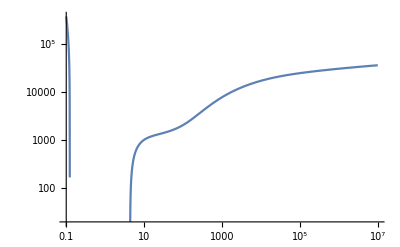

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mPion,1.37],{ϵ,.1,10^7}]
```

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

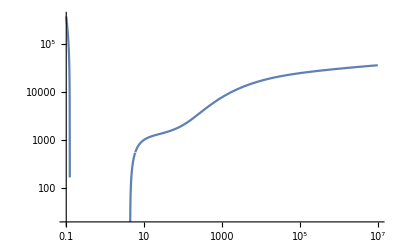
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

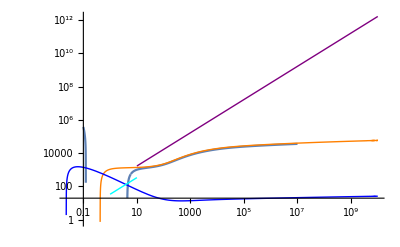

#### Low densities

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mPion,0.85],{ϵ,.1,10^7}],-Graphics-,PlotRange->All]
```

### Protons off electrons

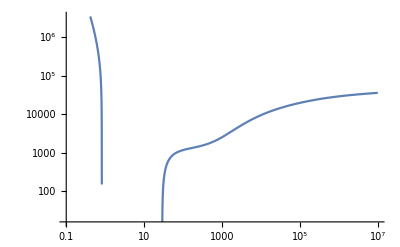

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mProton,1.37],{ϵ,.1,10^7}]
```

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

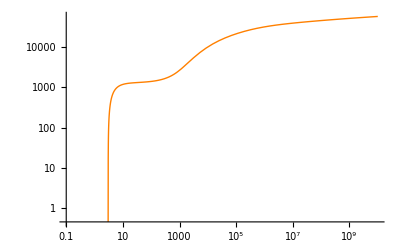
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

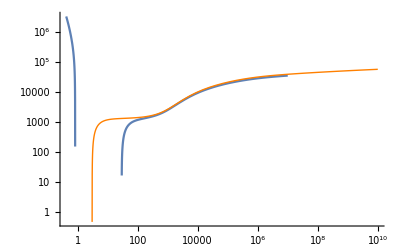

### Low densities

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

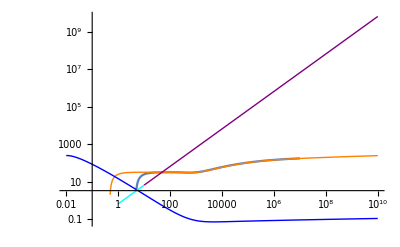

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mProton,0.85],{ϵ,.1,10^7}],-Graphics-,PlotRange->All]
```

Coulomb collisions of electrons off electrons

The derivation for coulomb collisions off electrons is the same as electrons off ions, except with different target number density. ω_kin also happens to be a factor of 2 smaller, presumably because of indistinguishability.

```mathematica
dEdxCoulombElectronsOffElectrons[ϵ_?NumericQ,Mwd_]:=NIntegrateTEMP[dσdωCoulomb[ω]ne ω,{ω,ωSCR,ωKIN}]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M]/2,
m->mElectron,M->mElectron,Z->-1(*electron targets*),ne->nElectronEffective[ω,Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}/.NIntegrateTEMP->NIntegrate;
```

### Electrons off electrons

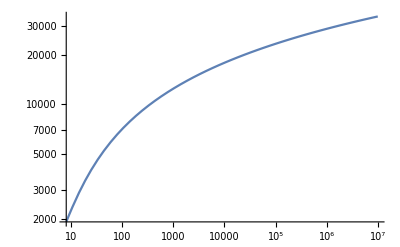

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffElectrons[ϵ,1.37],{ϵ,8,10^7}]
```

Comparing to Vijay’s results, we see they match pretty well

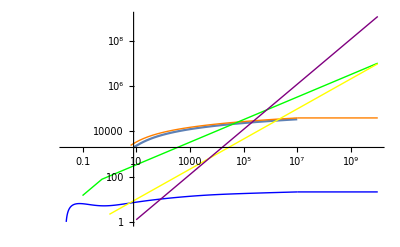

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

#### Low densities

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffElectrons[ϵ,1.37],{ϵ,8,10^7}]
```

-Graphics-

Comparing to Vijay’s results, we see they match pretty well

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

Compton and inverse compton scattering

## Compton scattering with Pauli-Blocking

### Electrons

The differential cross section for Compton scattering is

```mathematica
dσdΩCompton[cosθ_]:=α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]))//.{Sin[θ]^2->1-Cos[θ]^2,Cos[θ]->cosθ}//FullSimplify;
```

Integrating out the azimuthal dependence,

```mathematica
dσdcosθCompton[cosθ_]:=2π*dσdΩCompton[cosθ];
dσdcosθCompton[cosθ]
```

((cosθ^2+(k-cosθ k)/me+me/(k-cosθ k+me)) π α^2)/(k-cosθ k+me)^2

The energy transferred by a photon of energy k scattering at angle θ off an electron is

```mathematica
EtransferredCompton[cosθ_]:=k-k/(1+(k (1-cosθ))/me);
```

This exceeds the Fermi energy for angles

```mathematica
Solve[EtransferredCompton[cosθ]==Ef,cosθ]//FullSimplify
```

{{cosθ→1+(Ef me)/((Ef-k) k)}}

and smaller (and negative) values of cosθ.

Note the effective electron density is reduced in the Fermi sea. (see nElectronEffective defined along with the electron number density in the White Dwarf parameters section above.)

So the Compton stopping power on electrons is

```mathematica
dEdxCompton[ϵ_?NumericQ,Mwd_]:=Int[dσdcosθCompton[cosθ]n ω,{cosθ,-1,1}]//.{n->nElectronEffective[ω,Mwd],ω->EtransferredCompton[cosθ],Ef->EFermiMeV[Mwd],k->ϵ,me->mElectron,α->αval}/.Int->NIntegrate;
```

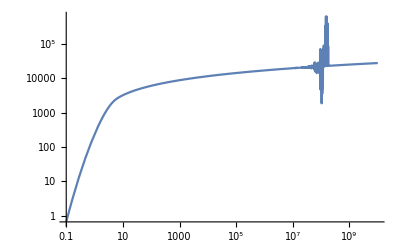

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*Quiet@dEdxCompton[ϵ,1.37],{ϵ,.1,10^10},PlotRange->All]
```

```mathematica
nElectronMeV[1.37]
```

6.95976

This matches Vijay’s result excellently.

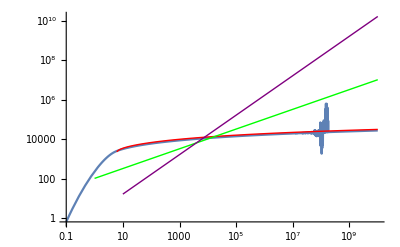

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

```mathematica
nElectronMeV[0.85]
```

0.0311932

For a low-mass white dwarf, comparing to Vijay’s result, this again matches excellently

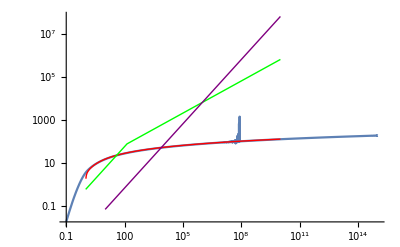

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*Quiet@dEdxCompton[ϵ,0.85],{ϵ,.1,10^15},PlotRange->All],-Graphics-]
```

### Protons

even more negligible.

## Inverse compton

negligible, because the photon number density is so much smaller than the electron number density.

Electron Bremsstrahlung (with LPM)

The cross-section for an election of energy ϵ to radiate a photon of energy k is given by the Bethe-Heitler formula

```mathematica
dσBHdkBremNoLPM=1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

where X_0=(4n Z^2 α^3/me^2 Log[Λ])^-1 is the radiation length and log Λ ∼ ∫1/b is a logarithmic form factor containing the maximum and minimum effective impact parameters allowed in the scatter. Integrating for the stopping power

```mathematica
dEdxBremNoLPM=Integrate[dσBHdkBremNoLPM*k*n,{k,0,ϵ}]
```

ϵ/X0

For the log, the max impact parameter is set by the screening length, and the min by the Compton wavelength. Here we see the “brem shutoff” at all but very low densities .... but we’ll ignore this and assume logΛ ~ 1 like Vijay has in his calculations, assuming this isn’t something to worry about.

```mathematica
Log[bmax/bmin]//.{bmax->λThomasFermi[Mwd],bmin->(2π)/mElectron,Mwd->0.4586}
```

0.000122986

```mathematica
X0Brem[Mwd_]:=(4n Z^2 α^3/me^2 logΛ)^-1/.{n->nIonMeV[Mwd],Z->ZCarbon,α->αval,me->mElectron,logΛ->1};
```

At high incident energies LPM suppression becomes relevant. This modifies the cross section at high energies (E>E_LPM) to be

```mathematica
dσBHdkBremWithLPM=√((ELPM ϵ)/(k(ϵ-k)))1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

for an LPM-suppressed stopping power

```mathematica
dEdxBremWithLPM=Integrate[dσBHdkBremWithLPM*k*n,{k,0,ϵ}]
```

(25 π √(ELPM/ϵ) ϵ)/(24 X0)

The LPM energy is

```mathematica
ELPMBrem[Mwd_]:=(me^2 X0 α)/(4π)/.{me->mElectron,α->αval,X0->X0Brem[Mwd]};
```

and we find the full stopping power to be

```mathematica
dEdxBrem[ϵ_,Mwd_]:=Piecewise[{{ϵ/X0,ϵ<ELPM},{(25π)/24(ELPM/ϵ)^(1/2)ϵ/X0,ϵ>ELPM}}]/.{X0->X0Brem[Mwd],ELPM->ELPMBrem[Mwd]};
```

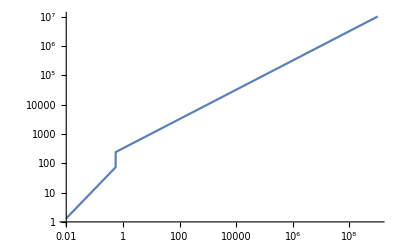

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxBrem[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9}]
```

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

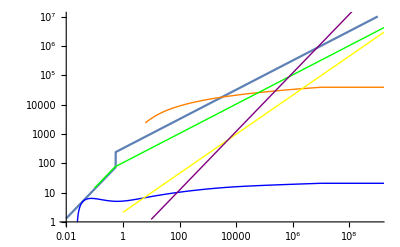

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

This again matches well, again differing by a factor of 3-4.

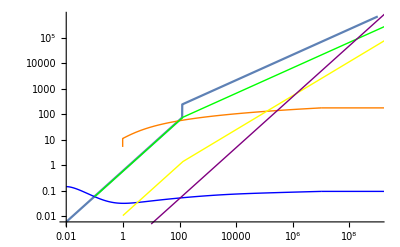

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxBrem[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9}],-Graphics-]
```

Pair production (with LPM)

The cross-section for a photon of energy ϵ to radiate an electron-positron pair with energies e and ϵ-e is given by a similar Bethe-Heitler formula

```mathematica
dσBHdkPP=1/(3ϵ n X0)(1+2(x^2+(1-x)^2))/.{x->e/ϵ};
```

where X_0=(4n Z^2 α^3/me^2 Log[Λ_pp])^-1 is a similar radiation length, only the log being different. (What is it??) Integrating for the stopping power

```mathematica
dEdxPPNoLPM=Integrate[dσBHdkPP ϵ n,{e,0,ϵ}]//FullSimplify
```

(7 ϵ)/(9 X0)

For the log ........

```mathematica
Log[bmax/bmin]
```

Log[bmax/bmin]

```mathematica
X0PP[Mwd_]:=(4n Z^2 α^3/me^2 logΛpp)^-1/.{n->nIonMeV[Mwd],Z->ZCarbon,α->αval,me->mElectron,logΛpp->1};
```

At high incident energies LPM suppression becomes relevant. This modifies the cross section at high energies (E>E_LPM) to be

```mathematica
dσBHdkPPwithLPM=√((ELPM ϵ)/(e(ϵ-e)))1/(3ϵ n X0)(1+2(x^2+(1-x)^2))/.{x->e/ϵ};
```

for a new stopping power

```mathematica
dEdxPPwithLPM=Integrate[dσBHdkPPwithLPM ϵ n,{e,0,ϵ}]//FullSimplify
```

(5 π √(ELPM/ϵ) ϵ)/(6 X0)

The LPM energy is the same, except with the new radiation length (Is this true???),

```mathematica
ELPMPP[Mwd_]:=(me^2 X0 α)/(4π)/.{me->mElectron,α->αval,X0->X0PP[Mwd]};
```

and we find the full stopping power to be

```mathematica
dEdxPP[ϵ_,Mwd_]:=Piecewise[{{(7 ϵ)/(9 X0),2m≤ϵ<ELPM},{(5π)/6(ELPM/ϵ)^(1/2)ϵ/X0,ϵ>ELPM},{0,ϵ<2m}}]/.{X0->X0PP[Mwd],ELPM->ELPMPP[Mwd],m->mElectron};
```

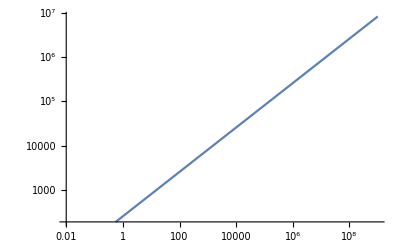

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPP[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9}]
```

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

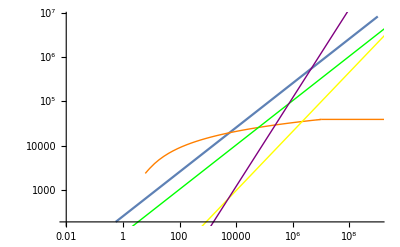

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

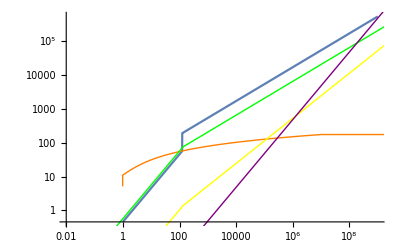

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPP[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9}],-Graphics-]
```

Direct pair production from electron scattering (with LPM)

Here we adapt directly the stopping power formula in Vijay’s notebook (no formulas are given explicitly in the paper) in a way to make it look similar to the previous radiative processes in this notebook. We find

```mathematica
dEdxDirectPP[ϵ_,Mwd_]:=Piecewise[{{(ELPM/ϵ)^(1/3)α ϵ/X0*3,ϵ≥ELPM},{α ϵ/X0*3,2m≤ϵ≤ELPM},{0,ϵ<2m}}]//.{X0->((4n Z^2 α^3)/m^2)^-1,ELPM->(m^2 X0 α)/(4π),α->αval,m->mElectron,Z->ZCarbon,n->nIonMeV[Mwd]}
```

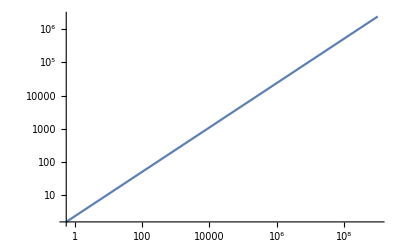

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxDirectPP[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9},PlotRange->All]
```

This matches Vijay’s results well, as we should hope

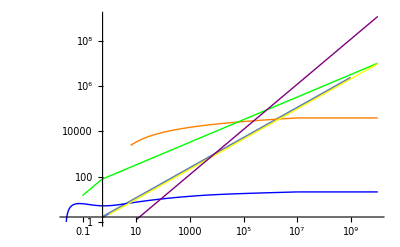

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

This matches Vijay’s results well, as we should hope

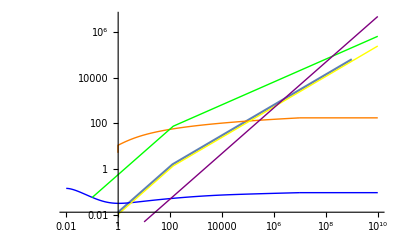

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxDirectPP[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9},PlotRange->All],-Graphics-]
```

# Generic constraints

Here we compute and plot constraints for transits, collisions, and decays for generic heavy dark matter candidates.

# Q-balls constraints

Here we compute and plot constraints for Q-balls specifically.

# Explosion energy with photon gas complications

```mathematica
NumGenerationsγA[ϵγ_,Mwd_]:=λγAShutoff/λγA//.{λγAShutoff->(ϵγ/(ne*TγAShutoff+TγAShutoff^4))^(1/3),λγA->1/(n*σγA)^-1,n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV,ne->nElectronMeV[Mwd], TγAShutoff->10}
```

```mathematica
NumGenerationsγA[10^5,1.37]
```

721538.

```mathematica
λγAShutoff//.{λγAShutoff->(ϵγ/(ne*TγAShutoff+TγAShutoff^4))^(1/3),λγA->1/(n*σγA)^-1,n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV,ne->nElectronMeV[Mwd], TγAShutoff->10}/.Mwd->1.37/.ϵγ->1
```

0.0463087

```mathematica
1/Quantity[1.,"Megaelectronvolts"] Quantity[1.,"ReducedPlanckConstant"]Quantity[1.,"SpeedOfLight"]//UnitConvert
```

1.97327×10^-13 m